20 Cálculo Vectorial
20.1 Dibujo de campos vectoriales

Se asocia un vector a cada punto

```mathematica
i={1,0}
j={0,1}
```

{1,0}

{0,1}

```mathematica
V=y*i-x*j
```

{y,-x}

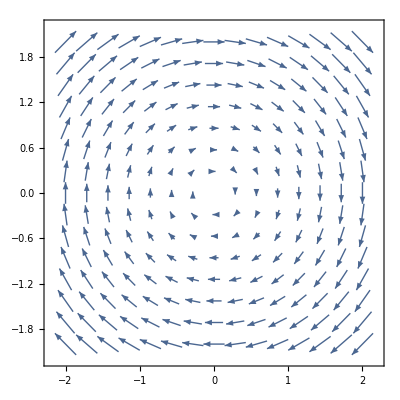

```mathematica
VectorPlot[V,{x,-2,2},{y,-2,2}]
```

```mathematica
V={2*x*y,4*x,5*z*y}
VectorPlot3D[V,{x,-2,2},{y,-2,2},{z,-2,2}]
```

{2 x y,4 x,5 y z}

-Graphics3D-

20.2 Gradiente, laplaciano y hessiano

```mathematica
f=x^2+y^2+z^2
```

x^2+y^2+z^2

```mathematica
g=x*y*z^6+3(x+y)*z^2
```

3 (x+y) z^2+x y z^6

Gradiente:

```mathematica
Grad[f,{x,y,z}]
Grad[g,{x,y,z}]
```

{2 x,2 y,2 z}

{3 z^2+y z^6,3 z^2+x z^6,6 (x+y) z+6 x y z^5}

```mathematica
D[f,{{x,y,z}}]
D[g,{{x,y,z}}]
```

{2 x,2 y,2 z}

{3 z^2+y z^6,3 z^2+x z^6,6 (x+y) z+6 x y z^5}

Laplaciano:

```mathematica
Laplacian[f,{x,y,z}]
Laplacian[g,{x,y,z}]
```

6

6 (x+y)+30 x y z^4

Hessiano:

```mathematica
D[f,{{x,y,z},2}]//MatrixForm
D[g,{{x,y,z},2}]//MatrixForm
```

(2 | 0 | 0
0 | 2 | 0
0 | 0 | 2)

(0 | z^6 | 6 z+6 y z^5
z^6 | 0 | 6 z+6 x z^5
6 z+6 y z^5 | 6 z+6 x z^5 | 6 (x+y)+30 x y z^4)

20.3 Divergencia, rotacional y jacobiano

```mathematica
V={3(x+y)z,5*x*y*z^3,8*x^2+3*z-7*y}
```

{3 (x+y) z,5 x y z^3,8 x^2-7 y+3 z}

Divergencia:

```mathematica
Div[V,{x,y,z}]
```

3+3 z+5 x z^3

Rotacional:

```mathematica
Curl[V,{x,y,z}]
```

{-7-15 x y z^2,-16 x+3 (x+y),-3 z+5 y z^3}

Jacobiano:

```mathematica
D[V,{{x,y,z}}]//MatrixForm
```

(3 z | 3 z | 3 (x+y)
5 y z^3 | 5 x z^3 | 15 x y z^2
16 x | -7 | 3)

20.4 Identidades vectoriales

```mathematica
Clear[f,g,V]
```

rot(grad(f))=OverVector[0]:

```mathematica
Curl[Grad[f[x,y,z],{x,y,z}],{x,y,z}]
```

{0,0,0}

div(grad(f))=lap(f):

```mathematica
Div[Grad[f[x,y,z],{x,y,z}],{x,y,z}]
```

f^(0,0,2)[x,y,z]+f^(0,2,0)[x,y,z]+f^(2,0,0)[x,y,z]

```mathematica
Laplacian[f[x,y,z],{x,y,z}]
```

f^(0,0,2)[x,y,z]+f^(0,2,0)[x,y,z]+f^(2,0,0)[x,y,z]

div(rot(f))=0:

```mathematica
V={f[x,y,z],g[x,y,z],h[x,y,z]}
```

{f[x,y,z],g[x,y,z],h[x,y,z]}

```mathematica
Div[Curl[V,{x,y,z}],{x,y,z}]
```

0

20.4 Identidades vectoriales

Calcular, en coordenadas esféricas, el gradiente de rCos[θ]Sin[ϕ]:

```mathematica
Grad[r*Cos[θ]*Sin[ϕ],{r,θ,ϕ},"Spherical"]
```

{Cos[θ] Sin[ϕ],-Sin[θ] Sin[ϕ],Cos[ϕ] Cot[θ]}